# Визуализация данных

## 1. Команды построения графиков. Примитивы и директивы двумерной графики.

2022205

Для построения графика функции одной переменной используется команда Plot. Ее первый аргумент — выражение с одной символьной переменной. Второй аргумент (итератор) — одномерный список, несущий информацию о границах, в которых должна изменяться переменная при построении графика.

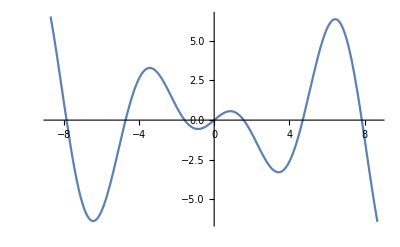

```mathematica
$TextStyle={FontSize->14};
Clear[l,k,g];
l={2,0,2,2,2,0,5};
k=√((∑_(i=1)^Length[l] l[[i]]^2)/Length[l]);
Clear [l]; l={2,2,2,2,5};
g=(∏_(i=1)^Length[l] l[[i]])^(1/Length[l]);
p1=Plot[Cos[x] x,{x,-2π-k,2π+g}]
```

Команда Plot позволяет изобразить на одном рисунке графики сразу нескольких функций для одной и той же области изменения их общего аргумента:

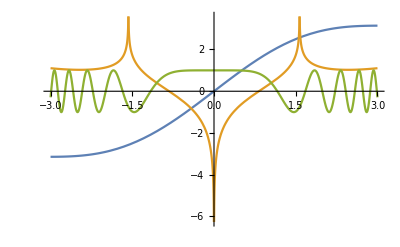

```mathematica
p2=Plot[{x+Sin[x],Log[Abs[x/(√Cos[x])]],Cos[x^3]},
                                                                                        {x,-3,3}]
```

Образец описания работы предыдущей команды.
Переменной р2 присваивается результат построения графиков 3-х функций (список функций{x+Sin[x],Log[Abs[x/(√Cos[x])]],Cos[x^3]}).
Переменная x меняется в пределах от -3 до 3.

Выполнить следующие команды

```mathematica
Clear[f1,x];
```

```mathematica
f1[x_]:=Which[x<-Pi/2||x>3Pi/2,x,x<Pi/2,Cos[x],x>Pi/2,Sin[2x]]
```

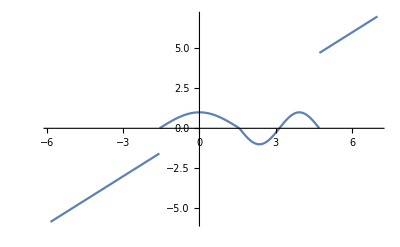

```mathematica
Plot[f1[x],{x,-4- (∑_(i=1)^Length[l] l[[i]])/Length[l],7},PlotRange->All]
```

Задание

В этой ячейке Описать работу предыдущих команд (см образец выше).
Функция f1 определяет, какой график будет построен. Это определяется с помощью команды Which (а именно, при x<-Pi/2 или x>3Pi/2 будет построен график y=x, при x<Pi/2 — y=Cos[x], а при x>Pi/2 будет построен график y=Sin[2x].
Функция Plot строит графики функций, определенных функцией f1.
Переменная x меняется в пределах от -4- (∑_(i=1)^Length[l] l[[i]])/Length[l] до 7.
PlotRange→All говорит о том, что по ось Oy будет такой, что будут видны все значения функций, которые определяются функциями.

Определим функцию tangentLine, которая рисует график выражения expr, содержащего  переменную x, и касательную к нему в заданной точке x0. Поскольку tangentLine фактически будет графической функцией, то добавим в число ее аргументов параметр opts, который позволит указывать произвольное количество графических опций.

```mathematica
tangentLine[f_, {x_, x0_}, opts___] :=
  Module[{df, p1},
    df = ReplaceAll[D[f, x], x -> x0]*
              (x - x0) + ReplaceAll[f, x -> x0];
    Plot[{f, df}, {x, x0 - 2, x0 + 2}, opts]  ]
```

Задание

В этой ячейке Описать, как работает 
  Module[{df, p1},    df = ReplaceAll[D[f, x], x -> x0]* (x - x0) + ReplaceAll[f, x -> x0];
    Plot[{f, df}, {x, x0 - 2, x0 + 2}, opts]
    
  Объявляются переменные df и p1 локально, затем записывается условие уравнение касательной: ReplaceAll[D[f, x], x -> x0]* (x - x0) + ReplaceAll[f, x -> x0]. ReplaceAll вычисляет производную и функцию в точке x0. Затем строится график на промежутке x0-2, x0+2, а opts испольлзуется для графических опций.

Построим с помощью tangentLine график функции sin(x)sin(x^2)и касательную к нему в точке 2/5 π.

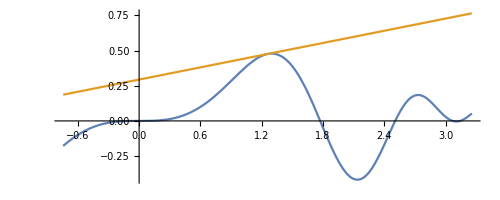

```mathematica
$TextStyle=FontSize->14;tangentLine[ 0.5Sin[x] Sin[x^2],{x,2Pi/5},AspectRatio->Automatic]
```

Задание

Выполнить построение для функции:  “среднее арифметическое всех цифр студенческого билета” * cos x *cos( x^2).

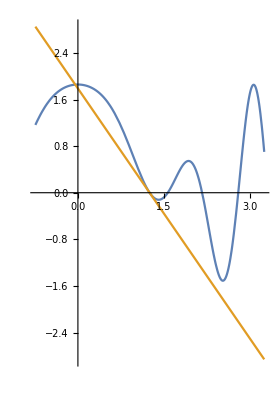

```mathematica
$TextStyle=FontSize->14;tangentLine[(∑_(i=1)^Length[l] l[[i]])/Length[l] Cos[x] Cos[x^2],{x,2Pi/5},AspectRatio->Automatic]
```

Опция AspectRatio со значением Automatic отвечает за то, чтобы в построенном изображении масштабы по координатным осям совпадали.

Задание

Установите разные масштабы по осям, например 2:1  и 1:2 и постройте эти графики.

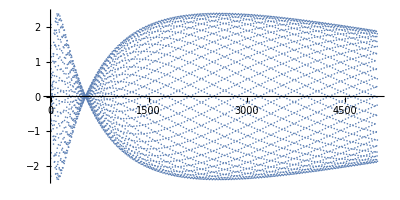

```mathematica
Clear [l]; l={2,2,2,2,5};
ListPlot[(∏_(i=1)^Length[l] l[[i]])^(1/Length[l])* Sin[Log[#]]*Sin[#]& /@Range[5000], AspectRatio->1/2]
```

Задание

В этой ячейке  описать работу этой команды: ListPlot[Sin[Log[#]]*Sin[#]& /@Range[5000]]
Строит график функции Sin[Log[x]]*Sin[x] по точкам

Выполнить следующие команды

```mathematica
Clear[f];
f[x_]:=If [x-1<0,(x-1)^2,(x-1)^2+1]
```

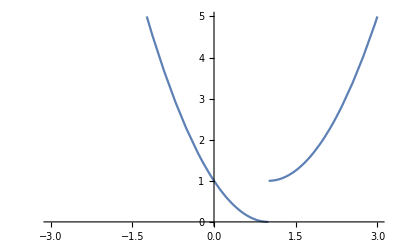

```mathematica
$TextStyle={FontSize->14};
Plot[Evaluate[f[x]],{x,-5,5},PlotRange->{{-3,3},{0,5}}]
```

Для построения двумерных графиков функций, заданных параметрически, используется команда ParametricPlot.

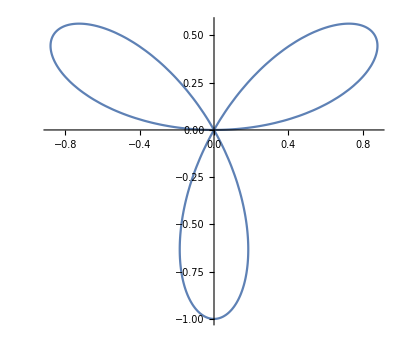

```mathematica
p4=ParametricPlot[{Cos[t] Sin[3 t], Sin[t] Sin[3 t]},{t,0,Pi}]
```

Визуализация содержимого числовых списков производится командой ListPlot. Единственным аргументом команды ListPlot может быть числовой одномерный список. В построенном графике по горизонтальной оси будут откладываться порядковые номера элементов списка, а по вертикальной — значения этих элементов.

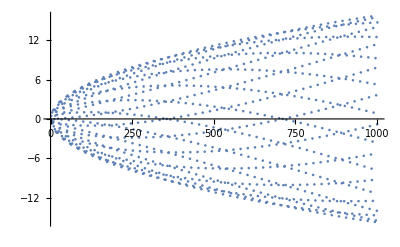

```mathematica
$TextStyle={FontSize->14};lst=Table[Sqrt[n]Sin[n]Cos[n],{n,0,1000}];
p8=ListPlot[lst]
```

Получив в качестве аргумента список числовых пар (двухэлементных списков), команда ListPlot изобразит точки с соответствующими парами координат.

{{-3,Cos[3]},{-5/2,Cos[5/2]},{-2,Cos[2]},{-3/2,Cos[3/2]},{-1,Cos[1]},{-1/2,Cos[1/2]},{0,1},{1/2,Cos[1/2]},{1,Cos[1]},{3/2,Cos[3/2]},{2,Cos[2]},{5/2,Cos[5/2]},{3,Cos[3]}}

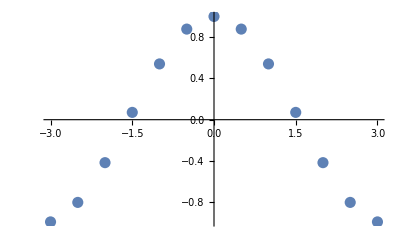

```mathematica
lst1=Table[{i,Cos[i]},{i,-3,3,1/2}]
p9=ListPlot[lst1,PlotStyle->PointSize[0.02]]
```

Опция PlotStyle в данном случае используется для установления размера выводимых точек в 2% от общей ширины рисунка.

Задание

В команде lst1=Table[{i,Cos[i]},{i,-“среднее геометрическое всех цифр студенческого билета”,“среднее ариф всех цифр студенческого билета”,1/2}] измените  шаг  индекса, а также опции PlotStyle и пересчитайте в новой ячейке р9

{{-2^(4/5) 5^(1/5),Cos[2^(4/5) 5^(1/5)]},{1/5-2^(4/5) 5^(1/5),Cos[1/5-2^(4/5) 5^(1/5)]},{2/5-2^(4/5) 5^(1/5),Cos[2/5-2^(4/5) 5^(1/5)]},{3/5-2^(4/5) 5^(1/5),Cos[3/5-2^(4/5) 5^(1/5)]},{4/5-2^(4/5) 5^(1/5),Cos[4/5-2^(4/5) 5^(1/5)]},{1-2^(4/5) 5^(1/5),Cos[1-2^(4/5) 5^(1/5)]},{6/5-2^(4/5) 5^(1/5),Cos[6/5-2^(4/5) 5^(1/5)]},{7/5-2^(4/5) 5^(1/5),Cos[7/5-2^(4/5) 5^(1/5)]},{8/5-2^(4/5) 5^(1/5),Cos[8/5-2^(4/5) 5^(1/5)]},{9/5-2^(4/5) 5^(1/5),Cos[9/5-2^(4/5) 5^(1/5)]},{2-2^(4/5) 5^(1/5),Cos[2-2^(4/5) 5^(1/5)]},{11/5-2^(4/5) 5^(1/5),Cos[11/5-2^(4/5) 5^(1/5)]},{12/5-2^(4/5) 5^(1/5),Cos[12/5-2^(4/5) 5^(1/5)]},{13/5-2^(4/5) 5^(1/5),Cos[13/5-2^(4/5) 5^(1/5)]},{14/5-2^(4/5) 5^(1/5),Cos[14/5-2^(4/5) 5^(1/5)]},{3-2^(4/5) 5^(1/5),Cos[3-2^(4/5) 5^(1/5)]},{16/5-2^(4/5) 5^(1/5),Cos[16/5-2^(4/5) 5^(1/5)]},{17/5-2^(4/5) 5^(1/5),Cos[17/5-2^(4/5) 5^(1/5)]},{18/5-2^(4/5) 5^(1/5),Cos[18/5-2^(4/5) 5^(1/5)]},{19/5-2^(4/5) 5^(1/5),Cos[19/5-2^(4/5) 5^(1/5)]},{4-2^(4/5) 5^(1/5),Cos[4-2^(4/5) 5^(1/5)]},{21/5-2^(4/5) 5^(1/5),Cos[21/5-2^(4/5) 5^(1/5)]},{22/5-2^(4/5) 5^(1/5),Cos[22/5-2^(4/5) 5^(1/5)]},{23/5-2^(4/5) 5^(1/5),Cos[23/5-2^(4/5) 5^(1/5)]},{24/5-2^(4/5) 5^(1/5),Cos[24/5-2^(4/5) 5^(1/5)]},{5-2^(4/5) 5^(1/5),Cos[5-2^(4/5) 5^(1/5)]}}

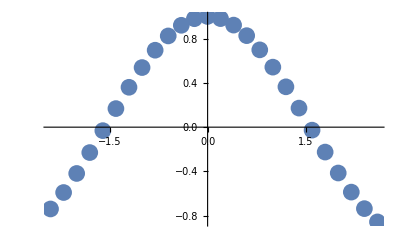

```mathematica
Clear[lst1, p9, l];
l={2,2,2,2,5};
lst1=Table[{i,Cos[i]},{i,-(∏_(i=1)^Length[l] l[[i]])^(1/Length[l]),(∑_(i=1)^Length[l] l[[i]])/Length[l],1/Length[l]}]
p9=ListPlot[lst1,PlotStyle->PointSize[0.03]]
```

## 2. Трехмерная графика.

Команда Plot3D для построения трехмерных графиков функций двух переменных имеет аналогичную форму записи с командой Plot, с той лишь разницей, что в ней необходимо указывать области изменения для двух переменных:

```mathematica
$TextStyle={FontSize->14};
p3=Plot3D[Sin[2x]*Sin[3x+y],
                                             {x,-1,1},{y,-3,3}]
```

Задание

Кликните правой кнопкой мыши по построенному графику. В меню проверьте работу всех пунктов, которые отвечают за просмотр.

Для построения трехмерных графиков функций, заданных параметрически, используется команда ParametricPlot3D.
Команда ParametricPlot3D может использоваться для построения как кривых (один параметр), так и поверхностей (два параметра).

```mathematica
p5=ParametricPlot3D[{Sin[t/8]Cos[t],Sin[t/8]Sin[t],t/8},{t,0,8Pi},PlotPoints->1000]
```

Задание

Команду p5=ParametricPlot3D[{Sin[t/8]Cos[t],Sin[t/8]Sin[t],t/“среднее геометрическое всех цифр студенческого билета”},{t,0,8Pi},PlotPoints→1000]  выполните в новой ячейке.

```mathematica
Clear[p5, l];
l={2,2,2,2,5};
p5=ParametricPlot3D[{Sin[t/8]Cos[t],Sin[t/8]Sin[t],t/(∏_(i=1)^Length[l] l[[i]])^(1/Length[l])},{t,0,8Pi},PlotPoints->1000]
```

-Graphics3D-

```mathematica
$TextStyle={FontSize->14};p6=ParametricPlot3D[{ Cos[p]+Sin[t] , Sin[p] + Cos[t],t},{p,0,2Pi},{t,-Pi,Pi}]
```

-Graphics3D-

Нечто среднее между двумерным и трехмерным графиком можно получить с помощью функции ContourPlot. Эта функция служит для построения контурного изображения трехмерной поверхности.

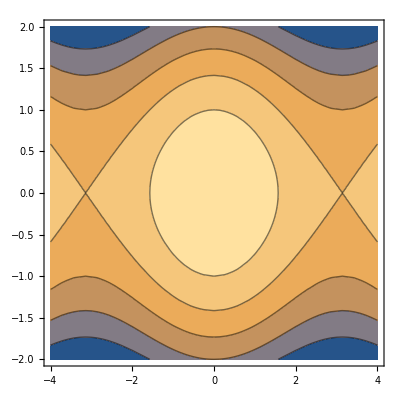

```mathematica
p7 = ContourPlot[Cos[x] - y^2, 
                    {x, -4, 4}, {y, -2, 2}]
```

Команды Plot, ParametricPlot, ParametricPlot3D позволяют выводить на одном рисунке графики нескольких функций одновременно. Для совмещения рисунков, полученных этими, а также и другими графическими командами, используется команда Show.

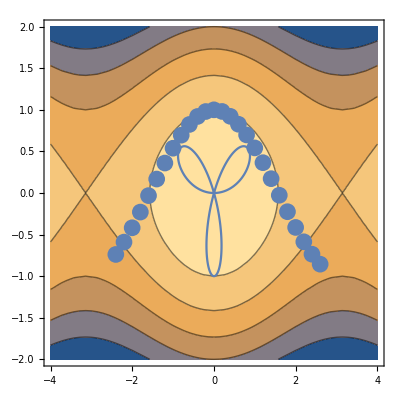

```mathematica
Show[p7,p4,p9]
```

Изображения перекрывают друг друга в том же порядке, в каком перечисляются соответствующие переменные.